# Sculpin & Smelt Encounter Rates

## Eden Forbes

```mathematica
ClearAll["Global`*"]
```

#### Parameter Declaration

```mathematica
(* Population Constants *)
mN= 10^-5; (* 0-0.25 per cm^2, Total mysid density - O'Malley et al. (2018) *)
sculN =0.001; (* Sculpin population density (#/cm^2) - Bowers et al. (1990) *)
smeltN =0.001; (* Smelt population density (#/cm^3) - Stritzel Thomson et al. (2011) *)

(* Size Constants *)
bmL = 1.7; (* Big mysid length in cm - Ramcharan et al. (1985), O'Malley & Stockwell (2019)*)
sculL = 13.0; (* Sculpin length in cm in Lake Ontario - Weidel et al. (2017) *)
sculD = 29.0; (* Sculpin detection radius in cm - Janssen (1990) *)
sculmin = 2.0; (* minimum sculppin detection radius in cm *)
smeltL = 10.0;  (* ~10, Smelt length in cm in Lake Ontario - Walsh et al. (2008) *)
smeltW = 50; (* Smelt Weight in g*)
smeltD = smeltL^1.1;  (* Smelt detection radius in cm - Gerritsen (1984) *)

(* Motion Constants *)
bmv = 3.0; (* ~0.5-5, Big mysid velocity in cm/sec - Bowers et al.(1990) *)
sculv = 4* sculL; (* Sculpin max velocity - cm/sec NEED *)
scultmax = 2.0; (* Sculpin time to max velocity in sec - arbitrary NEED *)
sculs= 10.0; (* Sculpin sampling interval in sec - arbitrary NEED *)
smeltv = 10*smeltL; (* Smelt velocity in cm/sec (bodylength/second) - Shuman & Coughlin (2018) *)
(* Migration Constants *)
tempdepth = 20; (* where is 14 C? Can fluctuate between 20-40m in the summer, in winter 14 or below everywhere *)
(* From Manley et al. (1999), O'Malley & Stockwell (2019) *)
lightdepth = 40;
dsens = 10^7;
```

## Functions

### Sculpin ER

```mathematica
(* Circles & Velo *)
Velo[s_,tmax_, maxv_]:=(maxv s^2)/(tmax + s^2);
Aint[tmax_, maxv_,s_, Dd_]:= -1/2 Velo[s,tmax, maxv]*s √(4 Dd^2-(Velo[s,tmax, maxv]*s )^2)+2 Dd^2 ArcCos[(Velo[s,tmax, maxv]*s)/(2 Dd)];

(* Continuous - Stationary *)
C2D[dens_,s_,tmax_,maxv_, Dd_]:= 2 dens Dd Velo[s,tmax,maxv];

(* Discrete - Stationary *)
D2D[dens_,s_, Dd_]:= (dens π Dd^2)/s;
(* Intermediate - Stationary *)
I2D[dens_,s_,tmax_, maxv_, Dd_]:=(dens (π Dd^2 - Re[Aint[tmax,maxv,s,Dd]]))/s;
(* Continuous - Mobile (same as M2D, but with sculpin params *)
C2Dm[dens_,u_,s_,tmax_,maxv_, Dd_]:=1/π 2 dens Dd(√((u-Velo[s,tmax,maxv])^2) EllipticE[-(4 u Velo[s,tmax,maxv])/(u-Velo[s,tmax,maxv])^2]+√((u+Velo[s,tmax,maxv])^2) EllipticE[(4 u Velo[s,tmax,maxv])/(u+Velo[s,tmax,maxv])^2]);
(* C2Dm when v = 0: - *)
FullSimplify[1/π 2 dens Dd(√((u-v)^2) EllipticE[-(4 u v)/(u-v)^2]+√((u+v)^2) EllipticE[(4 u v)/(u+v)^2]),v==0]
(* Discrete - Mobile *)
D2Dm[dens_,u_,s_,tmax_, maxv_, Dd_]:= 1/s 1/π 2 dens Dd(√((u-Velo[s,tmax,maxv])^2) EllipticE[-(4 u Velo[s,tmax,maxv])/(u-Velo[s,tmax,maxv])^2]+√((u+Velo[s,tmax,maxv])^2) EllipticE[(4 u Velo[s,tmax,maxv])/(u+Velo[s,tmax,maxv])^2]);
(* Intermediate - Mobile *)
I2Dm[dens_,u_,s_,tmax_, maxv_, Dd_]:=2 Dd dens u( Re[Aint[tmax,maxv,s,Dd]]/(π Dd^2))+D2Dm[dens,u,s,tmax, maxv, Dd](1-Re[Aint[tmax,maxv,s,Dd]]/(π Dd^2));
```

2 Dd dens √(u^2)

### Smelt & Mysis ER and EP

#### Stationary

```mathematica
S2D[dens_,v_, rad_]:= 2 dens rad v;
S3D[dens_,v_, rad_]:=  π rad^2 dens v;
```

#### Mobile

```mathematica
M2D[dens_, v_,u_,rad_]:=1/π 2 dens rad (√((u-v)^2) EllipticE[-(4 u v)/(u-v)^2]+√((u+v)^2) EllipticE[(4 u v)/(u+v)^2]);
M3D[dens_,v_,u_,rad_]:=  Piecewise[{{(π rad^2 dens)/3((u^2+3 v^2)/v), u<v},{(π rad^2 dens)/3((v^2+3 u^2)/u), u >= v}}];
```

### Migration

```mathematica
maxD[t_,dep_, dsens_]:= smeltD - (smeltD dep^4)/(dsens+ dep^4);
SmeltD[t_,dep_,dsens_]:=((maxD[t,dep,dsens]-1.5) Sin[0.261796(t-1) + 3Pi/2]+(1.5+maxD[t,dep,dsens]))/2;
```

```mathematica
mornstart1 = 6.5;
mornend1 = 7.5;
evestart1 = 18.5;
eveend1 = 19.5;
mornstart2 = 30.5;
mornend2 = 31.5;
evestart2 = 42.5;
eveend2 = 43.5;
```

```mathematica
depx[t_] := Piecewise[{
{tempdepth, 0<t<=mornstart1},
{(85-tempdepth)(t-mornend1 ) + 85, mornstart1 <t<=mornend1 },
{85, mornend1<t<=evestart1},
{-(85-tempdepth)(t-eveend1)+tempdepth, evestart1<t<=eveend1 },
{tempdepth, eveend1<t<=mornstart2},
{(85-tempdepth)(t-mornend2)+ 85, mornstart2<t<=mornend2},
{85, mornend2<t<=evestart2},
{-(85-tempdepth)(t-eveend2)+tempdepth, evestart2<t<=eveend2},
{tempdepth, eveend2<t<=48}
}];
```

```mathematica
benmig[t_, migprop_,sculN_, mN_,  s_]:= Piecewise[{
{sculN*(Re[I2Dm[(1-migprop)*mN/2,0,s,scultmax,sculv,sculD]]+C2Dm[(1-migprop)*mN/2,bmv,s,scultmax,sculv,sculmin]),0<t<mornend1},
{sculN*(Re[I2Dm[mN/2,0,s,scultmax,sculv,sculD]]+C2Dm[mN/2,bmv,s,scultmax,sculv,sculmin]),mornend1 <=t<=evestart1 },
{sculN*(Re[I2Dm[(1-migprop)*mN/2,0,s,scultmax,sculv,sculD]]+C2Dm[(1-migprop)*mN/2,bmv,s,scultmax,sculv,sculmin]),evestart1<t<mornend2},
{sculN*(Re[I2Dm[mN/2,0,s,scultmax,sculv,sculD]]+C2Dm[mN/2,bmv,s,scultmax,sculv,sculmin]),mornend2<=t<=evestart2},
{sculN*(Re[I2Dm[(1-migprop)*mN/2,0,s,scultmax,sculv,sculD]]+C2Dm[(1-migprop)*mN/2,bmv,s,scultmax,sculv,sculmin]),evestart2<t<48}
}];
pelmig[t_?NumericQ,mp_?NumericQ,sN_?NumericQ,mN_?NumericQ, v_?NumericQ]:= Piecewise[{
{sN*M3D[mp * mN/4,v,bmv,SmeltD[t,depx[t],dsens]],0<t<mornend1},
{0,mornend1<=t<=evestart1},
{sN*M3D[mp * mN/4,v,bmv,SmeltD[t,depx[t],dsens]],evestart1<t<mornend2},
{0,mornend2<=t<=evestart2},
{sN*M3D[mp * mN/4,v,bmv,SmeltD[t,depx[t],dsens]],evestart2<t<48}
}];
pelint[t_?NumericQ,mp_?NumericQ,sN_?NumericQ,mN_?NumericQ, v_?NumericQ]:= sN*M3D[mp * mN/4,v,bmv,SmeltD[t,depx[t],dsens]];
benint[t_?NumericQ,migprop_?NumericQ,mN_?NumericQ,sculN_?NumericQ,s_?NumericQ]:=sculN*(Re[I2Dm[(1-migprop)*mN/2,0,s,scultmax,sculv,sculD]]+C2Dm[(1-migprop)*mN/2,bmv,s,scultmax,sculv,sculmin]);
```

### Utility

```mathematica
restylePlot[p_,op:OptionsPattern[ListLinePlot]]:=ListLinePlot[Cases[Normal@p,Line[x__]:>x,∞],op,Options[p]]
```

## Analyses

### Encounter Rates

#### M2D

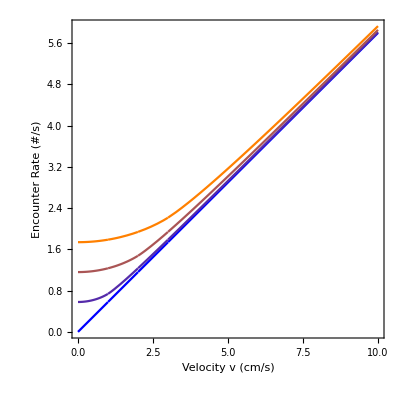

```mathematica
Plot[Evaluate@Table[Style[M2D[0.01,v,u,sculD],Blend[{Blue,Orange},u/3]],{u,0,3,1}],{v,0,10}, 
PlotRange->{All, {-0.2,All}},AspectRatio->1, Frame->True,FrameLabel->{"Velocity v (cm/s)","Encounter Rate (#/s)"}, LabelStyle->{Black,20}]
```

#### M3D

Power::infy: Infinite expression 1/0 encountered.

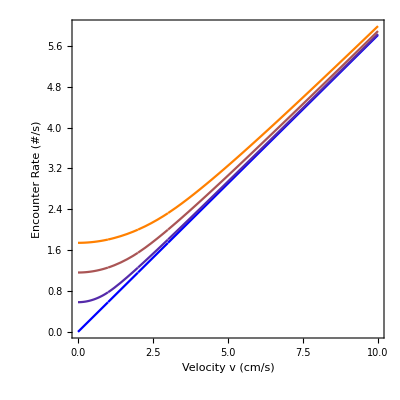

```mathematica
Plot[Evaluate@Table[Style[M3D[0.00022,v,u,sculD],Blend[{Blue,Orange},u/3]],{u,0,3,1}],{v,0,10}, 
PlotRange->{All, {-0.2,All}}, AspectRatio->1, Frame->True,FrameLabel->{"Velocity v (cm/s)","Encounter Rate (#/s)"}, LabelStyle->{Black,20}]
```

#### Sculpin

```mathematica
FindRoot[Aint[scultmax, sculv,s,sculD] == 0,{s,1}]
```

{s→1.80221}

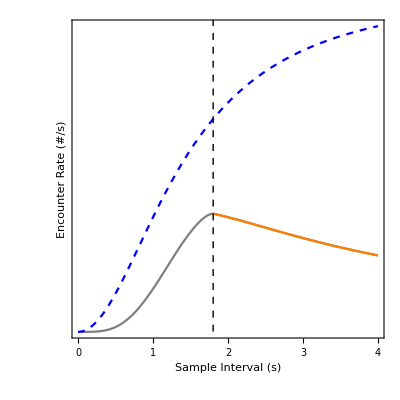

```mathematica
Show[
Plot[I2Dm[mN,0,s,scultmax, sculv, sculD],{s,0,4}, PlotStyle->Gray],
Plot[C2Dm[mN,0,s,scultmax, sculv, sculD],{s,0,4}, PlotStyle->{Blue,Dashed}],
Plot[D2Dm[mN,0,s,scultmax, sculv, sculD],{s,FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],4}, PlotStyle->Orange, PlotRange->{{1.8022,4},All}],
Graphics[{Dashed, Black, InfiniteLine[{{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],0},{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],50}}]}],
PlotRange->All, AspectRatio->1, Frame->True,FrameTicks->{True,False}, FrameLabel->{"Sample Interval (s)","Encounter Rate (#/s)"},LabelStyle->{20,Black}
]
```

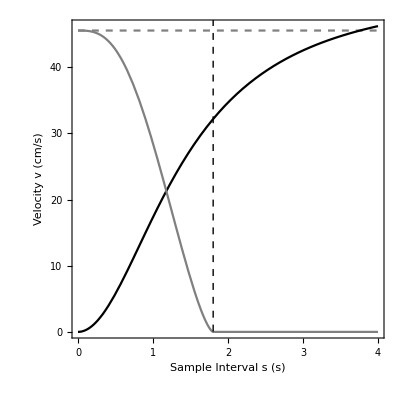

```mathematica
Show[
Plot[Pi sculD^2,{s,0,4}, PlotStyle->{Gray, Dashed}],
Plot[Velo[s,scultmax,sculv]2sculD,{s,0,4}, PlotStyle->Black],
Plot[Re[Aint[scultmax,sculv,s, sculD]],{s,0,4}, PlotStyle->Gray],
Graphics[{Dashed, Black, InfiniteLine[{{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],0},{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],50}}]}],
PlotRange->All, AspectRatio->1, Frame->True,FrameTicks->{Automatic,{{0,"0"},{580,"10"},{1160,"20"},{1740,"30"},{2320,"40"}}},FrameLabel->{"Sample Interval s (s)","Velocity v (cm/s)"},LabelStyle->{18,Black}
]
```

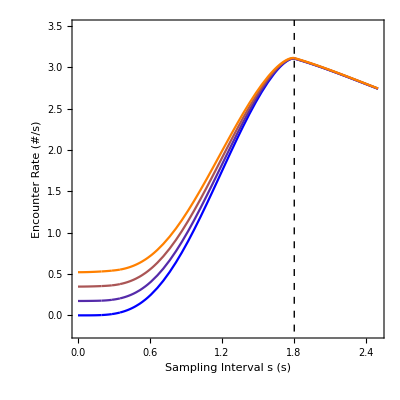

```mathematica
Show[
Plot[Evaluate@Table[Style[I2Dm[0.003,u,s,scultmax, sculv, sculD],Blend[{Blue,Orange},u/3]],{u,0,3,1}],{s,0,2.5}, 
PlotRange->{All, {-0.2,3.5}},AspectRatio->1, Frame->True,FrameLabel->{"Sampling Interval s (s)","Encounter Rate (#/s)"}, LabelStyle->{Black,20}],
Graphics[{Dashed, Black, InfiniteLine[{{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],0},{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],50}}]}]]
```

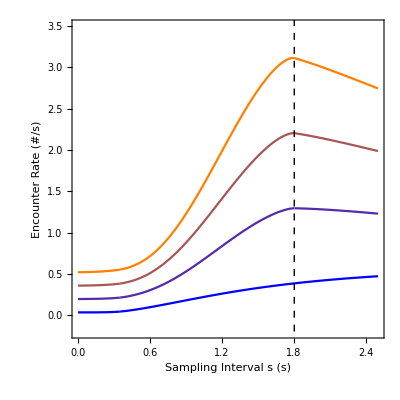

```mathematica
Show[
Plot[Evaluate@Table[Style[(I2Dm[0.003-f,bmv,s,scultmax, sculv, sculD]+C2Dm[f,bmv,s,scultmax,sculv,sculmin]),Blend[{Orange,Blue},f/0.003]],{f,0,0.003,0.001}],{s,0,2.5}, 
PlotRange->{All, {-0.2,3.5}},AspectRatio->1, Frame->True,FrameLabel->{"Sampling Interval s (s)","Encounter Rate (#/s)"}, LabelStyle->{Black,20}],
Graphics[{Dashed, Black, InfiniteLine[{{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],0},{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],50}}]}]]
```

## ER & Population

```mathematica
gg = Show[
Plot3D[sculN S2D[mN,Velo[s,scultmax,sculv],sculD],{s,0,3},{mN,0,0.01},PlotPoints->45,PlotLegends->Automatic,PlotStyle->{Opacity[0.35],Blue},
AspectRatio->1, LabelStyle->{Black,20}, Mesh->False],
Plot3D[sculN I2Dm[mN,0,s,scultmax, sculv, sculD],{s,0,3},{mN,0,0.01},PlotPoints->45,PlotLegends->Automatic,PlotStyle->{Opacity[0.35],Orange},
AspectRatio->1, LabelStyle->{Black,20}, Mesh->False],
PlotRange->All,Ticks->{Automatic,{{0.000,"0"},{0.005,"50"},{0.01,"100"}},Automatic}
]
```

-Graphics3D-

## ER & Migration

### Density

```mathematica
migprop = 0.75;
Show[
Plot3D[pelmig[t,migprop,smeltN,mN,15],{t,17,33},{mN,0,0.1},PlotPoints->80,PlotRange->All, Mesh->False, PlotStyle->{Blue,Opacity[0.5]}],
Plot3D[benmig[t,migprop,sculN,mN,0.9],{t,17,33},{mN,0,0.1},PlotPoints->80,PlotRange->All, Mesh->False, PlotStyle->{Orange,Opacity[0.5]}],
LabelStyle->{20,Black}, PlotLegends->Automatic, BoxRatios->{4, 4, 1},Ticks->{Automatic,{{0.000,"0"},{0.05,"500"},{0.1,"1000"}},Automatic}]
```

-Graphics3D-

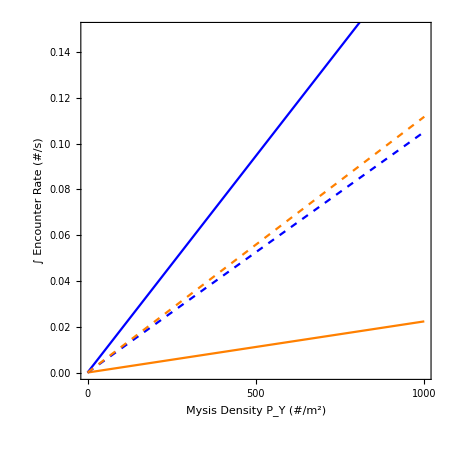

```mathematica
Show[
Plot[NIntegrate[pelint[t,0.9,smeltN,mN, 15],{t,18.5,31.5}],{mN,0,0.1}, PlotStyle->Blue],
Plot[13*benint[18.5,0.9,sculN,mN,0.9],{mN,0,0.1}, PlotStyle->Orange],
Plot[NIntegrate[pelint[t,0.5,smeltN,mN,15],{t,18.5,31.5}],{mN,0,0.1}, PlotStyle->{Blue,Dashed}],
Plot[13*benint[18.5,0.5,sculN,mN,0.9],{mN,0,0.1}, PlotStyle->{Orange,Dashed}],
Frame->True, FrameLabel->{"Mysis Density P_Y (#/m^2)","∫ Encounter Rate (#/s)"},LabelStyle->{20,Black},AspectRatio->1, PlotRange-> {All,{0,0.15}},FrameTicks->{{{0.000,"0"},{0.05,"500"},{0.1,"1000"}},Automatic}
]
```

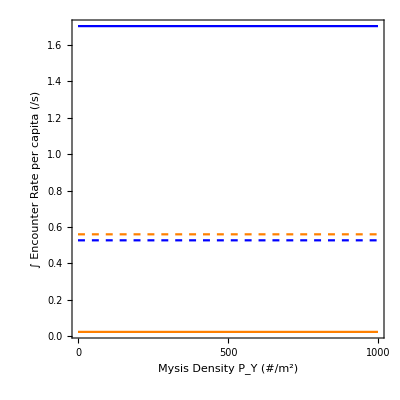

```mathematica
Show[
Plot[NIntegrate[pelint[t,0.9,smeltN,mN, 15],{t,18.5,31.5}]/mN*0.9,{mN,0,0.1}, PlotStyle->Blue],
Plot[13*benint[18.5,0.9,sculN,mN,0.9]/mN*0.1,{mN,0,0.1}, PlotStyle->Orange],
Plot[NIntegrate[pelint[t,0.5,smeltN,mN,15],{t,18.5,31.5}]/mN*0.5,{mN,0,0.1}, PlotStyle->{Blue,Dashed}],
Plot[13*benint[18.5,0.5,sculN,mN,0.9]/mN*0.5,{mN,0,0.1}, PlotStyle->{Orange,Dashed}],
Frame->True, FrameLabel->{"Mysis Density P_Y (#/m^2)","∫ Encounter Rate per capita (/s)"},LabelStyle->{20,Black},AspectRatio->1, PlotRange-> {All,All},FrameTicks->{{{0.000,"0"},{0.05,"500"},{0.1,"1000"}},Automatic}
]
```

### Behavior

```mathematica
mN = 0.05;
Show[
Plot3D[pelmig[t,migprop,smeltN,mN,Velo[s,scultmax,sculv]],{t,17,33},{s,0,3},PlotPoints->80,PlotRange->All, Mesh->False, PlotStyle->{Blue,Opacity[0.5]}],
Plot3D[benmig[t,migprop,sculN,mN,s],{t,17,33},{s,0,3},PlotPoints->80,PlotRange->All, Mesh->False, PlotStyle->{Orange,Opacity[0.5]}],
LabelStyle->{20,Black}, PlotLegends->Automatic, BoxRatios->{4, 4, 1}, Ticks->{Automatic,Automatic,Automatic}]
```

-Graphics3D-

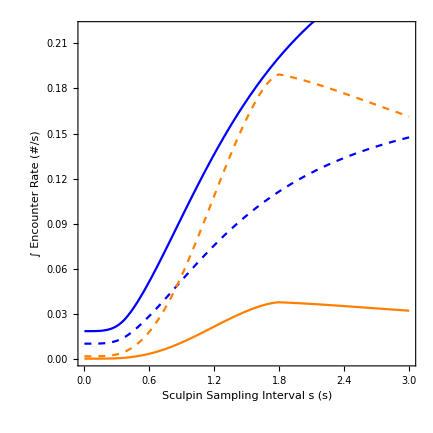

```mathematica
Show[
Plot[NIntegrate[pelint[t,0.9,smeltN,mN, Velo[s,scultmax,sculv]],{t,18.5,31.5}],{s,0,3}, PlotStyle->Blue],
Plot[13*benint[19.5,0.9,sculN,mN,s],{s,0,3}, PlotStyle->Orange],
Plot[NIntegrate[pelint[t,0.5,smeltN,mN, Velo[s,scultmax,sculv]],{t,18.5,31.5}],{s,0,3}, PlotStyle->{Blue,Dashed}],
Plot[13*benint[19.5,0.5,sculN,mN,s],{s,0,3}, PlotStyle->{Orange,Dashed}],
Frame->True, FrameLabel->{"Sculpin Sampling Interval s (s)","∫ Encounter Rate (#/s)"},LabelStyle->{20,Black},AspectRatio->1, PlotRange->{All,{0,0.22}}
]
```

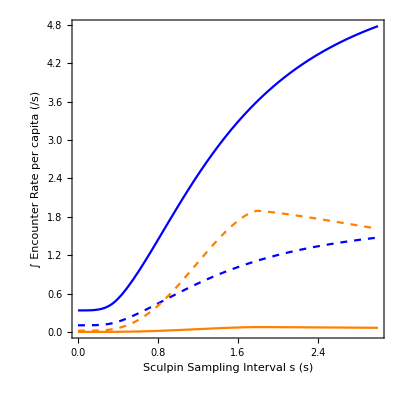

```mathematica
Show[
Plot[NIntegrate[pelint[t,0.9,smeltN,mN, Velo[s,scultmax,sculv]]/mN*0.9,{t,18.5,31.5}],{s,0,3}, PlotStyle->Blue],
Plot[13*benint[19.5,0.9,sculN,mN,s]/mN*0.1,{s,0,3}, PlotStyle->Orange],
Plot[NIntegrate[pelint[t,0.5,smeltN,mN, Velo[s,scultmax,sculv]]/mN*0.5,{t,18.5,31.5}],{s,0,3}, PlotStyle->{Blue,Dashed}],
Plot[13*benint[19.5,0.5,sculN,mN,s]/mN*0.5,{s,0,3}, PlotStyle->{Orange,Dashed}],
Frame->True, FrameLabel->{"Sculpin Sampling Interval s (s)","∫ Encounter Rate per capita (/s)"},LabelStyle->{20,Black},AspectRatio->1, PlotRange->All
]
```

### Migration Proportion

```mathematica
mN = 0.05;
Show[
Plot3D[pelmig[t,migprop,smeltN,mN,15],{t,17,33},{migprop,0,1},PlotPoints->40,PlotRange->All, Mesh->False, PlotStyle->{Blue,Opacity[0.5]}],
Plot3D[benmig[t,migprop,sculN,mN,0.9],{t,17,33},{migprop,0,1},PlotPoints->40,PlotRange->All, Mesh->False, PlotStyle->{Orange,Opacity[0.5]}],
LabelStyle->{20,Black}, PlotLegends->Automatic,BoxRatios->{4, 4, 1}, Ticks->{Automatic,Automatic,{{0.000,"0.00"},0.01,0.02}}]
```

-Graphics3D-

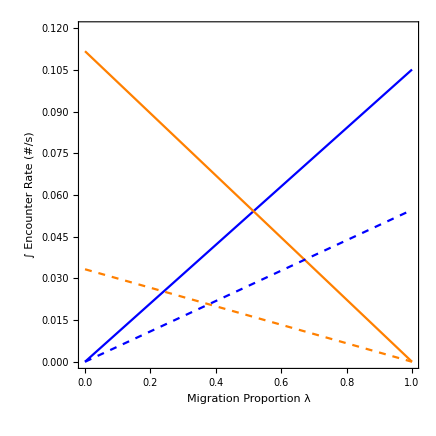

```mathematica
Show[
Plot[NIntegrate[pelint[t,migprop,smeltN,mN, 15],{t,18.5,31.5}],{migprop,0,1}, PlotStyle->Blue],
Plot[13*benint[19.5,migprop,sculN,mN,0.9],{migprop,0,1}, PlotStyle->Orange],
Plot[NIntegrate[pelint[t,migprop,smeltN,mN, 7.5],{t,18.5,31.5}],{migprop,0,1}, PlotStyle->{Blue,Dashed}],
Plot[13*benint[19.5,migprop,sculN,mN,0.58],{migprop,0,1}, PlotStyle->{Orange,Dashed}],
Frame->True, FrameLabel->{"Migration Proportion λ","∫ Encounter Rate (#/s)"},LabelStyle->{20,Black},AspectRatio->1, PlotRange->{All,{0,0.12}}
]
```

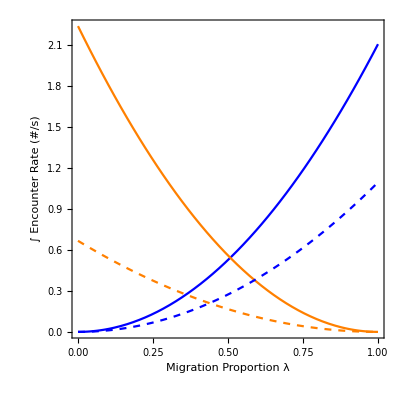

```mathematica
Show[
Plot[NIntegrate[pelint[t,migprop,smeltN,mN, 15],{t,18.5,31.5}]/mN*migprop,{migprop,0,1}, PlotStyle->Blue],
Plot[13*benint[19.5,migprop,sculN,mN,0.9]/mN*(1-migprop),{migprop,0,1}, PlotStyle->Orange],
Plot[NIntegrate[pelint[t,migprop,smeltN,mN, 7.5],{t,18.5,31.5}]/mN*migprop,{migprop,0,1}, PlotStyle->{Blue,Dashed}],
Plot[13*benint[19.5,migprop,sculN,mN,0.58]/mN*(1-migprop),{migprop,0,1}, PlotStyle->{Orange,Dashed}],
Frame->True, FrameLabel->{"Migration Proportion λ","∫ Encounter Rate (#/s)"},LabelStyle->{20,Black},AspectRatio->1, PlotRange->{All,All}
]
```

```mathematica
Clear[migprop]
p1 = Plot[
FindRoot[NIntegrate[pelint[t,migprop,smeltN,mN, Velo[s,scultmax,sculv]],{t,18.5,31.5}]/mN*migprop == 13*benint[19.5,migprop,sculN,mN,s]/mN*(1-migprop),{migprop,0.5}][[1]][[2]],
{s,0,3},PlotStyle->{Blue,Dashed}];
p2 = Plot[
FindRoot[NIntegrate[pelint[t,migprop,smeltN,mN, Velo[s,scultmax,sculv]],{t,18.5,31.5}] == 13*benint[19.5,migprop,sculN,mN,s],{migprop,0.5}][[1]][[2]],
{s,0,3},PlotStyle->Blue];
p3 = Plot[
FindRoot[NIntegrate[pelint[t,migprop,smeltN,mN, Velo[0.1*s,scultmax,sculv]],{t,18.5,31.5}]/mN*migprop == 13*benint[19.5,migprop,sculN,mN,s]/mN*(1-migprop),{migprop,0.5}][[1]][[2]],
{s,0,3},PlotStyle->{Orange,Dashed}];
p4 = Plot[
FindRoot[NIntegrate[pelint[t,migprop,smeltN,mN, Velo[0.1*s,scultmax,sculv]],{t,18.5,31.5}] == 13*benint[19.5,migprop,sculN,mN,s],{migprop,0.5}][[1]][[2]],
{s,0,3},PlotStyle->Orange];
```

NIntegrate::inumr: The integrand pelint[t,migprop,0.001,0.05,9.76544×10^-8] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

NIntegrate::inumr: The integrand pelint[t,migprop,0.001,0.05,9.76544×10^-10] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

```mathematica
p5 = Plot[
FindRoot[NIntegrate[pelint[t,migprop,smeltN,mN, Velo[s,scultmax,sculv]],{t,18.5,31.5}]/mN*migprop == 13*benint[19.5,migprop,sculN,mN,0.1*s]/mN*(1-migprop),{migprop,0.5}][[1]][[2]],
{s,0,3},PlotStyle->{Black,Dashed}];
p6 = Plot[
FindRoot[NIntegrate[pelint[t,migprop,smeltN,mN, Velo[s,scultmax,sculv]],{t,18.5,31.5}] == 13*benint[19.5,migprop,sculN,mN,0.1*s],{migprop,0.5}][[1]][[2]],
{s,0,3},PlotStyle->Black];
```

NIntegrate::inumr: The integrand pelint[t,migprop,0.001,0.05,9.76544×10^-8] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

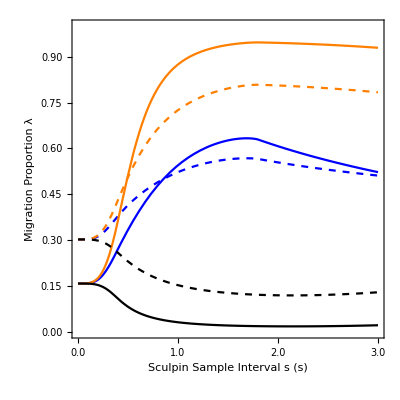

```mathematica
Show[
p1,
p2,
p3,
p4,
p5,
p6,
AxesOrigin->{0,0},AspectRatio->1,PlotRange->{All,{0,1}}, Frame->True,FrameLabel->{"Sculpin Sample Interval s (s)","Migration Proportion λ"}, LabelStyle->{16,Black},
FrameTicks->{{{0.00,"0.0"},{1.0,"1.0"},{2.0,"2.0"},{3.0,"3.0"}},Automatic}
]
```

```mathematica
FindRoot[NIntegrate[pelint[t,migprop,smeltN,mN, Velo[1,scultmax,sculv]],{t,18.5,31.5}]/mN*migprop == 13*benint[19.5,migprop,sculN,mN,1]/mN*(1-migprop),{migprop,0.5}][[1]][[2]]
```

NIntegrate::inumr: The integrand pelint[t,migprop,0.001,0.05,17.3333] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

0.522553

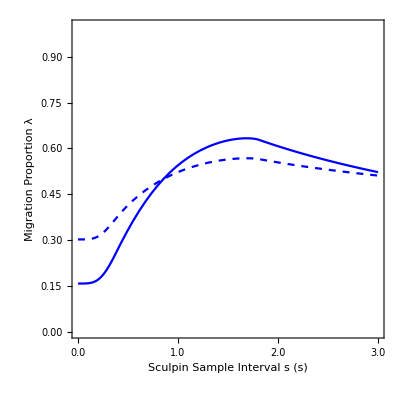

```mathematica
Show[
p1,
p2,
AxesOrigin->{0,0},AspectRatio->1,PlotRange->{All,{0,1}}, Frame->True,FrameLabel->{"Sculpin Sample Interval s (s)","Migration Proportion λ"}, LabelStyle->{16,Black},
FrameTicks->{{{0.00,"0.0"},{1.0,"1.0"},{2.0,"2.0"},{3.0,"3.0"}},Automatic}
]
```

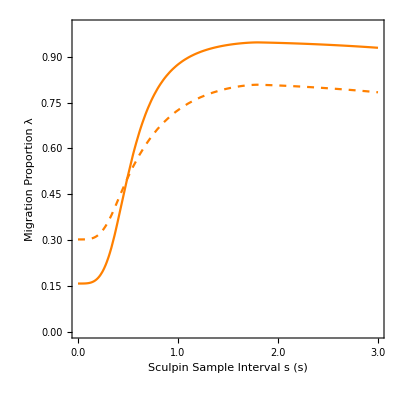

```mathematica
Show[
p3,
p4,
AxesOrigin->{0,0},AspectRatio->1,PlotRange->{All,{0,1}}, Frame->True,FrameLabel->{"Sculpin Sample Interval s (s)","Migration Proportion λ"}, LabelStyle->{16,Black},
FrameTicks->{{{0.00,"0.0"},{1.0,"1.0"},{2.0,"2.0"},{3.0,"3.0"}},Automatic}
]
```

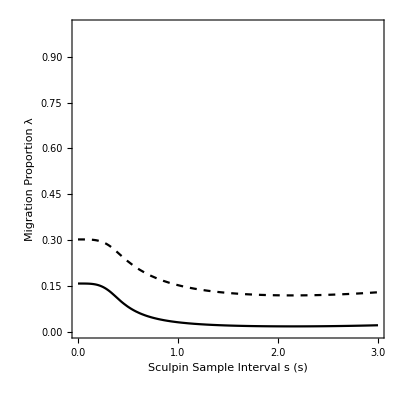

```mathematica
Show[
p5,
p6,
AxesOrigin->{0,0},AspectRatio->1,PlotRange->{All,{0,1}}, Frame->True,FrameLabel->{"Sculpin Sample Interval s (s)","Migration Proportion λ"}, LabelStyle->{16,Black},
FrameTicks->{{{0.00,"0.0"},{1.0,"1.0"},{2.0,"2.0"},{3.0,"3.0"}},Automatic}
]
```